# Project 1 : Solving Kepler' s Equation

## Task 1

```mathematica
f[M_,EA_,e_] := EA - e*Sin[EA] -M
df[EA_,e_]=D[f[M,EA,e],EA];
```

```mathematica
evalues = {0,0.25,0.5,0.75,0.99};
mvalues = Array[# &,100,{0,2 Pi}];
```

```mathematica
data = {};
For[i=1,i<=Length[evalues],i++,rootslist={};
For[k=1,k<=Length[mvalues],k++,xnew=mvalues[[k]];
For[j=1,j<=100,j++;xold=xnew;
xnew=xold-f[mvalues[[k]],xold,evalues[[i]]]/df[xold,evalues[[i]]];
If[xnew==0.||Abs[(xnew - xold)/xnew]>=0.0005,Break[]]];
rootslist = Append[rootslist,xnew]; ];
data = Append[data,rootslist];]
```

```mathematica
pdata=Table[Transpose[{mvalues,data[[i]]}],{i,Length[data]}];
```

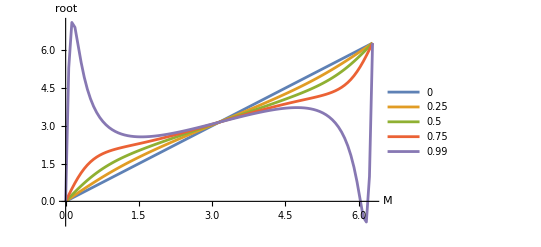

```mathematica
ListPlot[pdata,Joined->True,PlotLegends->evalues,AxesLabel->{"M","root"}]
```

## Task 2

```mathematica
LE[M_,e_,n_]:=M+Sum[(e^i/(i!))*(D[Sin[x]^i,{x,i-1}]/.{x->M}),{i,1,n}]
```

```mathematica
LE5[M_,e_]:=TrigReduce[LE[M,e,5]]
LE10[M_,e_]:=TrigReduce[LE[M,e,10]]
```

```mathematica
p13=ListPlot[pdata[[3]],Joined->True,PlotStyle->Red,PlotStyle->Red,PlotLegends->LineLegend[{Red},{"data"}]];
p15=ListPlot[pdata[[5]],Joined->True,PlotRange->All,PlotStyle->Red,PlotLegends->LineLegend[{Red},{"data"}]];
```

```mathematica
p21=Plot[{LE5[M,0.5],LE10[M,0.5]},{M,0,2*Pi},PlotStyle->{Green,Blue},PlotLegends->{"Ls5","Ls10"}];
p22=Plot[{LE5[M,0.99],LE10[M,0.99]},{M,0,2*Pi},PlotStyle->{Green,Blue},PlotLegends->{"Ls5","Ls10"}];
```

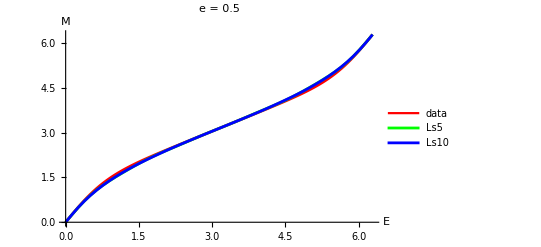

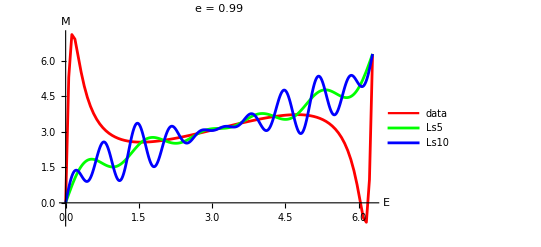

```mathematica
Show[{p13,p21},AxesLabel->{"E","M"},PlotLabel->"e = 0.5"]
Show[{p15,p22},AxesLabel->{"E","M"},PlotLabel->"e = 0.99"]
```

(Wintner 1941, Moulton 1970, Henrici 1974, Finch 2003) . Surprisingly, this series diverges for e > 0.6627434193 ... (From Wolfram MathWorld)

## Task 3

```mathematica
gE[x_]:=M+e*Sin[x]
```

```mathematica
CE [MM_,ee_,x_,NN_]:=Apply[Composition,Array[gE&,NN]][x]/.{M->MM,e->ee}
```

```mathematica
TE[M_,e_,x_,a_,n_]:=Sum[(D[CE[M,e,x,n+1],{x,i}]/.{x->a})*(x-a)^i/(i!),{i,0,n}]
```

```mathematica
TE5 [M_,e_]=Simplify[TE[M,e,e,0,5]];
TE10[M_,e_]=Simplify[TE[M,e,e,0,10]];
```

```mathematica
p31=Plot[{TE5[M,0.5],TE10[M,0.5]},{M,0,2*Pi},PlotStyle->{Purple,Red},PlotLegends->{"Ts5","Ts10"}];
p32=Plot[{TE5[M,0.99],TE10[M,0.99]},{M,0,2*Pi},PlotStyle->{Purple,Red},PlotLegends->{"Ts5","Ts10"}];
```

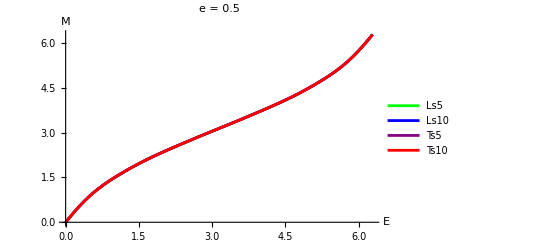

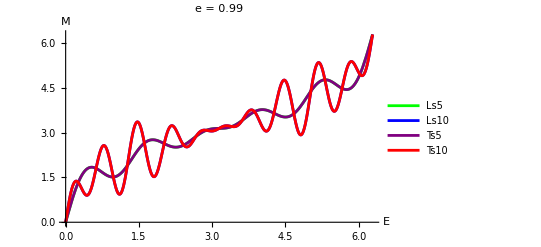

```mathematica
Show[{p21,p31},AxesLabel->{"E","M"},PlotLabel->"e = 0.5"]
Show[{p22,p32},AxesLabel->{"E","M"},PlotLabel->"e = 0.99"]
```

## Task 4

```mathematica
BJ[n_,z_,NN_]:=Sum[(-1)^i*(z/2)^(n+2*i)/(i!*(n+i)!),{i,0,NN}]
```

```mathematica
Plot[{BJ[1,x,20],BJ[2,x,20],BJ[3,x,20],BJ[4,x,20],BJ[5,x,20]},{x,0,15},PlotLabels->{"BJ1","BJ2","BJ3","BJ4","BJ5"},AxesLabel->{"x"}]
```

-Graphics-

```mathematica
BFE[M_,e_,MM_,NN_] :=M+Sum[2*BJ[j,j*e,MM]*Sin[j*M]/j,{j,1,NN}]
```

```mathematica
BFE5[M_,e_] =BFE[M,e,20,5] ; 
BFE10[M_,e_] =BFE[M,e,20,10] ;
```

```mathematica
p41=Plot[{BFE5[M,0.5],BFE10[M,0.5]},{M,0,2*Pi},PlotStyle->{Purple,Brown},PlotLegends->{"Bs5","Bs10"}];
p42=Plot[{BFE5[M,0.99],BFE10[M,0.99]},{M,0,2*Pi},PlotStyle->{Purple,Brown},PlotLegends->{"Bs5","Bs10"}];
```

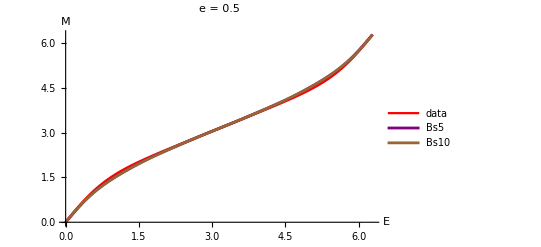

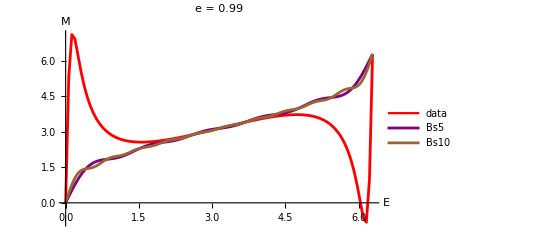

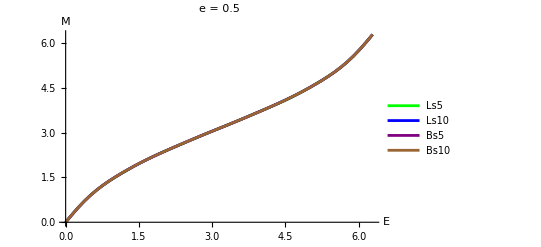

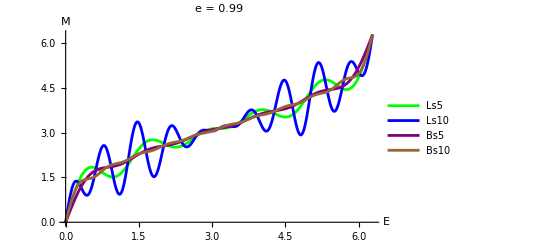

```mathematica
Show[{p13,p41},AxesLabel->{"E","M"},PlotLabel->"e = 0.5"]
Show[{p15,p42},AxesLabel->{"E","M"},PlotLabel->"e = 0.99"]
Show[{p21,p41},AxesLabel->{"E","M"},PlotLabel->"e = 0.5"]
Show[{p22,p42},AxesLabel->{"E","M"},PlotLabel->"e = 0.99"]
```